## Mathematical Determination of Righting Moment vs Heel Angle

Nathan Weil

In order to find the Angle of Vanishing Stability (AVS) of our boat design, we had to first calculate net torque on the boat at different heel angles. The AVS is the angle at which a boat cannot return itself to upright, and flips upside down. Due to its design, a boat’s buoyant force shifts deeper into the water as it lists, creating a righting moment which pushes the boat back towards level. The AVS is the point at which the center of buoyancy (COB) passes underneath the center of mass (COM) and creates a reverse righting moment which pushes the boat upside down.

-Graphics-

Figure 1: These free body diagrams show a simplified version of the relationship between the heel angle (angle of the deck relative to the water) and the resultant torque. When the boat is level, there is no righting moment because the buoyant force and the force of gravity are equal, opposite and acting along the same line. However, as the heel angle increases, the COB shifts to the right and a torque around the center of mass is created. When the boat reaches its AVS, the torque again reaches zero, as the COB passes under the COM. As the heel angle increases past the AVS, the torque is reversed and pushes the boat further upside down to an inverted stable equilibrium.

Fixed Global Variables

BoatCurve | y=3x^2/23
BoatDensity | 0.3 g/ml
MassBallast | 500 g
COBalast | {0,0cm}
MastMass | 96 g
MastCom | {0,25cm}
BoatLength | 45 cm
BoatWidth | 20cm
BoatHeight | 13cm

In order to find the AVS and better understand the behavior of our boat design, we need to plot the relationship between the torque created by the shifting COB and the heel angle. The first step in this process is to calculate the boat’s mass using its density, the density and location of the ballast, and the density and location of the aluminum mast.

totalMass = N[BoatLength*Integrate[BoatDensity,{x,y}∈boat]+MassBalast+MastMass]

This equation takes the variables BoatLength, BoatDensity, and the region boat, and finds the integral of the region with respect to both x and y. The region boat is a mathematical region defined by BoatCurve for lower y values and BoatHeight for higher y values. This finds the area of the region, and multiplies it by the length of the boat and BoatDensity to find the total mass. The mass of the ballast and the mast are also added to the total weight. Mathematica’s N[...] function returns a decimal approximation of the result.

disp = BoatLength*Integrate[.997, {x, y} ∈ under];

Next, we need to calculate the boat’s displacement (disp) by integrating the density of the water with respect to x and y bounded by the region under. This region is defined as the intersection between the region boat and the region water, which is bounded on the top by a line y = Tan(x) + d. d is the draft height, the distance between the origin at the bottom of the boat and the y intercept of the water line.

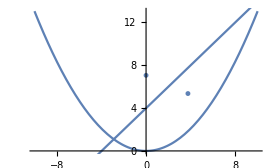

Figure 2: Plot of the BoatCurve, the water line, the COM and the COB at a heel angle of 45 degrees. The draft in this plot is 4 cm.

Next, we need to calculate the center of mass in order to find the point the boat pivots around. The equation for finding the center of mass is the following:

com = 1/totalMass∫∫∫_R ρ{x,y} dV

com = 1/totalMass*(RegionCentroid[boat]*mass+MassBalast*COBallast+MastMass*MastCom)

This can be implemented in Mathematica by using the RegionCentroid[...] function, which finds the geometric center of a region, in this case, the center of the region boat. boat is a region defined by BoatCurve on the bottom and y = BoatHeight on top. Because we assume the boat has uniform density, the geometric center of the boat is the boat’s center of mass. To get the boat’s overall center of mass, we can average the product of the masses and centers of mass.

draft = N[d/.FindRoot[disp==mass,{d,-30,30},AccuracyGoal→3][[1]], 3];

The draft height is calculated by setting the displacement equal to the mass of the boat and using the Mathematica function FindRoot[...] to find the intercept. The range {d, -30, 30} as well as the AccuracyGoal statement are used to speed up the process so that it takes less time when running multiple iterations.

cob = Append[RegionCentroid[under/.{d→draft}],0];

Now that we have calculated the draft, the COB can now be calculated using the RegionCentroid[...] function used above. The draft is plugged into the function for under region which updates its upper bound (the waterline) to have the correct y intercept. The centroid of this region is the center of mass of the water the boat displaces, which is also the center of buoyancy.

F_B=ρVg = F_g=mg

buoyancy = mass*98/10*{-Sin[theta Degree],Cos[theta Degree],0};

Because the buoyancy must be equal and opposite to the force of gravity in order for the boat to be in equilibrium, the magnitude of the force of buoyancy must be equal to the magnitude of the force of gravity. The force vectors of buoyancy can be calculated by multiplying the mass of the boat by 9.8 (acceleration due to gravity), and a vector that translates the resulting number into component vectors on the x and y axes.

torque = Cross[cob-com,buoyancy][[3]];

Finally, torque can be calculated by finding the cross product of the difference of the COB and the COM, and the buoyancy vector calculated above. The output is a torque in Nm along the boat’s axis. All of the above equations can be combined into a Mathematica module that can be run for multiple heel angles. A plot of heel angle vs righting torque can be created by running the module for a range of heel angles between 0 and 180 degrees.

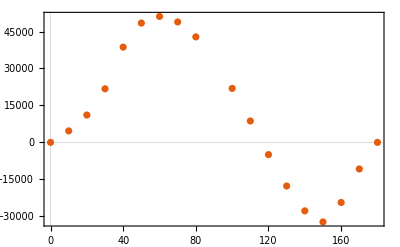

This plot shows heel angle in degrees on the x axis and torque along the y axis. As the boat nears 110 degrees, the curve crosses the x axis with a negative slope, meaning it is in unstable equilibrium, and at the AVS. The angle of vanishing stability for this particular boat is 110 degrees. In the next two days, we hope to increase this above the 120 degree minimum using a slightly different hull shape and different distribution of mass. Also, it is visible that the curve has a smaller slope near 0 degrees, meaning the righting moment is small when the boat is upright. This should be increased to keep the boat floating level when upright.